```mathematica
Clear["Global`*"]
```

```mathematica
(*Funktionen*)
GiveX[l_,y_]:=Extract[l,Position[l,{xs_,ys_}/;ys==y]][[1,1]]
GiveX[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;ys>=Range[[1]]&&ys<=Range[[2]]]][[1,1]]
GiveY[l_,x_]:=Extract[l,Position[l,{xs_,ys_}/;xs==x]][[1,2]]
GiveY[l_,Range_List]:=Extract[l,Position[l,{xs_,ys_}/;xs>=Range[[1]]&&xs<=Range[[2]]]][[1,2]]
GiveXY[l_,z_]:=Extract[l,Position[l,{xs_,ys_,zs_}/;zs==z]][[1]][[{1,2}]]
FindMaximumList[l_]:={GiveX[l,Max[l]],Max[l]}(*Annahme: y>x*)
CheckEq[l1_List,l2_List,n_]:=Sequence[]
CheckEq[l1_List,l2_List,n_]:=l1[[n]]/;(l1[[n,2]]≥l2[[n,2]]&&l1[[n,2]]≤l2[[n+5,2]])||(l1[[n,2]]≤l2[[n,2]]&&l1[[n,2]]≥l2[[n+5,2]])
CheckEqPoints[l1_List,l2_List,start_:1]:=Flatten[Table[{CheckEq[l1,l2,n]},{n,start,Length[l1]-5}]/.{}->Sequence[],1]
```

```mathematica
(*Parameter*)
M=60.; (*Masse des Gegengewichts*)
m=0.5; (*Masse des Geschosses*)
d=0.1; (*Dicke des Wurfarms*)
Tm=0.;(*Plot und Integrations Range*)
Tp=1.5;
θ0=-Pi/4; (*Startwinkel des Wurfarms, wenn keine Einschränkung aus Geometrie*)
n=2000;(*Anzahl der Auswertungspunkte*)
(*Konstanten*)
g=9.81;
(*Dichte*)
ρ=100.;
```

```mathematica
(*Startwerte*)
L0=17; (*Länge des Wurfarms*)
r0=15;(*Länge der Schlinge*)
h0=3.4;(*Länge der Aufhängung des Gegengewichts*)
x0=3;(*Abstand Aufhängung des Wurfarms zum SP, guter Start: L0/4*)
```

```mathematica
(*abgeleitete Parameter*)
L1[L_,x_]:=L/2-x
L2[L_,x_]:=L/2+x
μ[L_]:=L d^2 ρ
V[L_,x_]:=M g L1[L,x] - m g L2[L,x] - μ[L] g x
i[L_,x_]:=μ[L](1/12 L^2+x^2)+m L2[L,x]^2+M L1[L,x]^2
```

```mathematica
(*abgeleitete Parameter aus den Startwerten*)
L1[L0,x0]//N
L2[L0,x0]//N
L1[L0,x0]/L2[L0,x0]//N
r0/(L1[L0,x0]+L2[L0,x0])//N
r0/L2[L0,x0]//N
h0/L1[L0,x0]//N
```

5.5

11.5

0.478261

0.882353

1.30435

0.618182

```mathematica
(*Einschränkung an den Startwinkel aus Geometrie*)
(*Achtung: θstart muss größer als Pi/4=0.785 sein, sonst wird der optimale Abwurfwinkel nie erreicht*)
(*θstart[L_,h_,x_]:=Re[-ArcCos[(L1[L,x] Sin[Pi/4]+h)/L2[L,x]]HeavisideTheta[L2[L,x]-L1[L,x] Sin[Pi/4]-h]+θ0 HeavisideTheta[L1[L,x] Sin[Pi/4]+h-L2[L,x]]]*)
θstart[L_,h_,x_]:=θ0
θstart[L0,h0,x0];
```

```mathematica
(*Lösung der DGL*)
s[L_,r_,h_,x_]:=NDSolve[{i[L,x] θ''[t]==M L1[L,x] h φ''[t]Sin[φ[t]+θ[t]]+M L1[L,x] h φ'[t]^2 Cos[φ[t]+θ[t]]-m L2[L,x] r ψ''[t]Cos[ψ[t]-θ[t]]+m L2[L,x] r ψ'[t]^2 Sin[ψ[t]-θ[t]]+V[L,x] Cos[θ[t]],h φ''[t]==L1[L,x] θ''[t]Sin[φ[t]+θ[t]]+L1[L,x] θ'[t]^2 Cos[φ[t]+θ[t]]-g Sin[φ[t]],r ψ''[t]==-L2[L,x] θ''[t]Cos[ψ[t]-θ[t]]-L2[L,x] θ'[t]^2 Sin[ψ[t]-θ[t]]-g Cos[ψ[t]],θ[0]==θstart[L,h,x],θ'[0]==0,φ[0]==0,φ'[0]==0,ψ[0]==-Pi+0.1,ψ'[0]==0},{θ,φ,ψ},{t,Tm,Tp}]
```

```mathematica
(*Plots*)
Pv[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Geschossgeschwindigkeit",AxesLabel->{"t","v(t)"}]]
Ppsi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[ψ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Psi",AxesLabel->{"t","ψ(t)"}]]
Pphi[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[φ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Phi",AxesLabel->{"t","ψ(t)"}]]
Pth[L_,r_,h_,x_,t1_:0,t2_:0]:=Block[{S},S=s[L,r,h,x];Plot[Evaluate[θ[t]/.S],{t,Tm,Tp},PlotRange->All,GridLines->{{{t1,Red},{t2,Green}},None},PlotLabel->"Theta",AxesLabel->{"t","θ(t)"}]]
```

```mathematica
thList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(θ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
psiList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(ψ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
phiList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(φ[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*Betrag der Geschossgeschwindigkeit*)
vList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,Re[(Sqrt[(L2[L,x] θ'[t])^2+(r ψ'[t])^2+2 L2[L,x]ψ'[t]θ'[t]Cos[ψ[t]-θ[t]]]/.S)[[1]]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*x-Komponente der Geschossgeschwindigkeit*)
vxList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*y-Komponente der Geschossgeschwindigkeit*)
vyList[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{t,(L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t]/.S)[[1]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*Integrierte Wurfweite*)
sWurf[vx_,vy_,h_]:=vx(vy+Sqrt[2 g h +vy^2])/g
sWurfList[L_,r_,h_,x_]:=Block[{S,vx,vy,H},
S=s[L,r,h,x];
vx=((-L2[L,x] Sin[θ[t]] θ'[t]-r Sin[ψ[t]] ψ'[t])/.S)[[1]];
vy=((L2[L,x] Cos[θ[t]] θ'[t]+r Cos[ψ[t]] ψ'[t])/.S)[[1]];
H=((L Sin[θ[t]]+h)/.S)[[1]];
Table[{t,Re[sWurf[vx,vy,H]]},{t,Tm,Tp,(Tp-Tm)/n}]]
(*Beste Abwurfzeit nach der Wurfweite*)
(*tmax[L_,r_,h_,x_]:=FindMaximumList[sWurfList[L,r,h,x]][[1]]*)
(*Beste Abwurfzeit nach Geschossgeschwindigkeit*)
tmax[L_,r_,h_,x_]:=FindMaximumList[vList[L,r,h,x]][[1]]
smax[L_,r_,h_,x_]:=GiveY[sWurfList[L,r,h,x],tmax[L,r,h,x]]
vmax[L_,r_,h_,x_]:=GiveY[vList[L,r,h,x],tmax[L,r,h,x]]
```

1.5

119.677

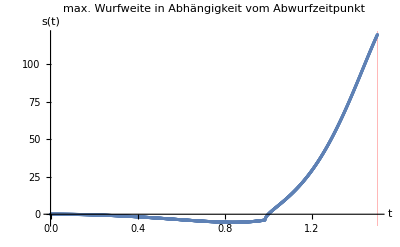

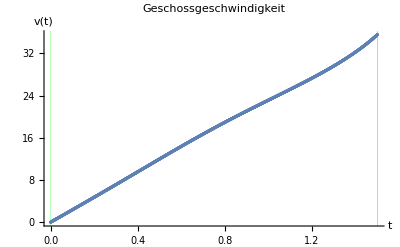

```mathematica
t0=tmax[L0,r0,h0,x0]
s0=smax[L0,r0,h0,x0]
Show[ListPlot[sWurfList[L0,r0,h0,x0],PlotRange->All,GridLines->{{{t0,Red}},None},PlotLabel->"max. Wurfweite in Abhängigkeit vom Abwurfzeitpunkt",AxesLabel->{"t","s(t)"}]]
Show[Pv[L0,r0,h0,x0,t0],ListPlot[vList[L0,r0,h0,x0]]]
(*Show[Pth[L0,r0,h0,x0,t0],ListPlot[thList[L0,r0,h0,x0]]]
Show[Ppsi[L0,r0,h0,x0,t0],ListPlot[psiList[L0,r0,h0,x0]]]*)
```

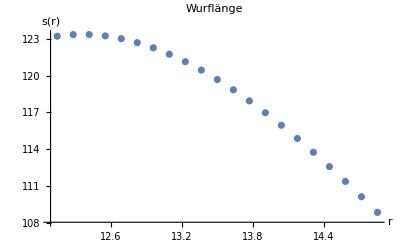

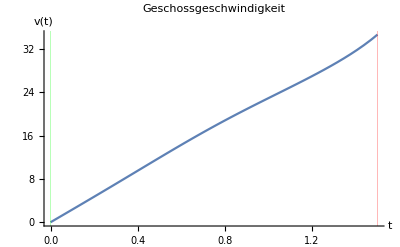

Abwurfzeitpunkt t0 = 1.5

neuer Startwert für L0 = 17

neuer Startwert für r0 = 12.42

neuer Startwert für h0 = 3.4

neuer Startwert für x0 = 3

vmax = 34.6913

smax = 123.331

```mathematica
(*1D Analyse in r*)
smaxr=Table[{r,smax[L0,r,h0,x0]},{r,0.9r0,1.1r0,0.1r0/10}];
ListPlot[smaxr,PlotLabel->"Wurflänge",AxesLabel->{"r","s(r)"}]
rmax=FindMaximumList[Abs[smaxr]][[1]];
r0=rmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
```

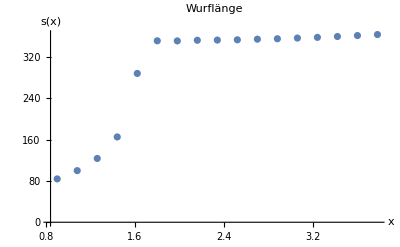

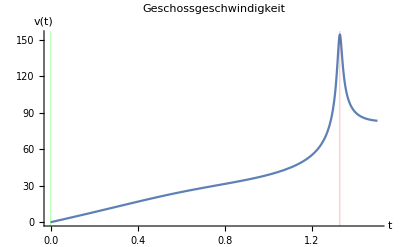

Abwurfzeitpunkt t0 = 1.3275

neuer Startwert für L0 = 17

neuer Startwert für r0 = 18.7

neuer Startwert für h0 = 3.4

neuer Startwert für x0 = 3.78

vmax = 154.133

smax = 363.293

```mathematica
(*1D Analyse in x*)
smaxx=Table[{x,smax[L0,r0,h0,x]},{x,0.3x0,1.3 x0,0.6x0/10}];
ListPlot[smaxx,PlotLabel->"Wurflänge",AxesLabel->{"x","s(x)"}]
xmax=FindMaximumList[Abs[smaxx]][[1]];
x0=xmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]
```

```mathematica
(*1D Analyse in L*)
(*smaxL=Table[{L,smax[L,r0,h0,x0]},{L,0.9L0,1.1 L0,0.2L0/10}];
ListPlot[smaxL,PlotLabel->"Wurflänge",AxesLabel->{"L","s(L)"}]
Lmax=FindMaximumList[Abs[smaxL]][[1]];
L0=Lmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]*)
```

```mathematica
(*Notiz: Optimierung über h konvergiert nicht. h sollte deshalb so groß wie technisch möglich gewählt werden.*)
(*1D Analyse in h*)
(*smaxh=Table[{h,smax[L0,r0,h,x0]},{h,0.9h0,1.1 h0,0.2h0/10}];
ListPlot[smaxh,PlotLabel->"Wurflänge",AxesLabel->{"h","s(h)"}]
hmax=FindMaximumList[Abs[smaxh]][[1]];
h0=hmax;
t0=tmax[L0,r0,h0,x0];
Pv[L0,r0,h0,x0,t0]
Print["Abwurfzeitpunkt t0 = ",t0]
Print["neuer Startwert für L0 = ",L0]
Print["neuer Startwert für r0 = ",r0]
Print["neuer Startwert für h0 = ",h0]
Print["neuer Startwert für x0 = ",x0]
Print["vmax = ",vmax[L0,r0,h0,x0]]
Print["smax = ",smax[L0,r0,h0,x0]]*)
```

```mathematica
Tend=t0;
(*Vektoren*)
r1List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(L2[L,x]Cos[θ[t]])/.S][[1]],Evaluate[(L2[L,x]Sin[θ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r2List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(L2[L,x]Cos[θ[t]]+r Cos[ψ[t]])/.S][[1]],Evaluate[(L2[L,x]Sin[θ[t]]+r Sin[ψ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r3List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(-L1[L,x]Cos[θ[t]])/.S][[1]],Evaluate[(-L1[L,x]Sin[θ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
r4List[L_,r_,h_,x_]:=Block[{S},S=s[L,r,h,x];Table[{Evaluate[(-L1[L,x]Cos[θ[t]]-h Sin[φ[t]])/.S][[1]],Evaluate[(-L1[L,x]Sin[θ[t]]-h Cos[φ[t]])/.S][[1]]},{t,Tm,Tend,0.01}]]
Manipulate[
Show[ListPlot[{r2List[L0,r0,h0,x0],r1List[L0,r0,h0,x0]},PlotRange->{{-L2[L0,x0]-r0,L2[L0,x0]+r0},{-L2[L0,x0]-r0,L2[L0,x0]+r0}},Frame->True,ImageSize->{600,600},AspectRatio->1],Graphics[Line[{r4List[L0,r0,h0,x0][[Round[n]]],r3List[L0,r0,h0,x0][[Round[n]]],{0,0},r1List[L0,r0,h0,x0][[Round[n]]],r2List[L0,r0,h0,x0][[Round[n]]]}]]],{n,1,Length[r1List[L0,r0,h0,x0]]}]
```

Part::partw: Part 141 of {{-1.48492,0.484924},{-1.48492,0.484646},{-1.48492,0.483811},{-1.48493,0.482419},{-1.48493,0.480472},{-1.48493,0.47797},«39»,{-1.52186,-0.0711934},{-1.52485,-0.0967953},{-1.52798,-0.123067},{-1.53126,-0.150019},{-1.53467,-0.177659},«69»} does not exist.

Part::partw: Part 141 of {{-1.48492,1.48492},{-1.4852,1.48465},{-1.48604,1.48381},{-1.48743,1.48242},{-1.48937,1.48046},{-1.49187,1.47795},{-1.49492,1.47486},«38»,{-1.92247,0.845055},{-1.93538,0.815053},{-1.94798,0.784459},{-1.96024,0.753293},{-1.97214,0.721575},«69»} does not exist.

Part::partw: Part 141 of {{9.97021,-9.97021},{9.97208,-9.96834},{9.97768,-9.96273},{9.98702,-9.95337},{10.0001,-9.94025},{10.0168,-9.92335},{10.0373,-9.90265},«38»,{12.908,-5.67394},{12.9947,-5.4725},{13.0793,-5.26708},{13.1616,-5.05782},{13.2415,-4.84486},«69»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 141 of {{-0.956715,-0.0432845},{-0.956715,-0.0435307},{-0.956716,-0.0442691},{-0.956716,-0.0454997},{-0.956718,-0.0472224},{-0.956722,-0.049437},«39»,{-0.989123,-0.554707},{-0.991633,-0.578805},{-0.994255,-0.603539},{-0.99699,-0.628913},{-0.999837,-0.654931},«56»} does not exist.

Part::partw: Part 141 of {{-0.956715,0.956715},{-0.956962,0.956469},{-0.9577,0.95573},{-0.958928,0.954498},{-0.960645,0.95277},{-0.962847,0.950544},«39»,{-1.29315,0.397956},{-1.3008,0.372204},{-1.30802,0.345961},{-1.3148,0.319242},{-1.3211,0.292058},«56»} does not exist.

Part::partw: Part 141 of {{1.56766,-1.56766},{1.56806,-1.56725},{1.56927,-1.56604},{1.57128,-1.56402},{1.57409,-1.56119},{1.5777,-1.55754},«39»,{2.11893,-0.652083},{2.13146,-0.609886},{2.1433,-0.566886},{2.1544,-0.523104},{2.16473,-0.478561},«56»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 141 of {{-0.3267,0.205861},{-0.341081,0.197214},{-0.355462,0.187866},{-0.369844,0.177799},{-0.384226,0.166995},«38»,{-0.702282,-0.619254},{-0.676206,-0.627803},{-0.650784,-0.637442},{-0.625998,-0.648159}} does not exist.

Part::partw: Part 141 of {{-0.3267,0.565861},{-0.341239,0.557214},{-0.356054,0.547866},{-0.371088,0.537797},{-0.386282,0.526989},«38»,{-0.348485,-0.552711},{-0.321024,-0.5691},{-0.294916,-0.583058},{-0.269939,-0.595033}} does not exist.

Part::partw: Part 141 of {{0.7695,-1.33281},{0.803744,-1.31245},{0.83864,-1.29043},{0.87405,-1.26671},{0.909838,-1.24126},«37»,{0.889383,1.25599},{0.820813,1.30184},{0.756132,1.34044},{0.694636,1.37332},{0.635808,1.40152}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.